```mathematica
$HistoryLength=0;
```

```mathematica
Needs["FourierSeries`"];ParallelNeeds["FourierSeries`"]
```

```mathematica
Needs[#<>"`",NotebookDirectory[]<>"wlPackages/"<>#<>".wl"]&~Scan~{"BinaryIcon","InverseLaplace",(*"PhysicsClusterUSYD",*)"Figures"}
```

```mathematica
NestedMap=ResourceFunction["ParallelOuter"]["MapFunction"->ResourceFunction["ParallelMapMonitored"]];
```

```mathematica
W[x_?NumericQ,s_?NumericQ,α_?NumericQ,d_?NumericQ]:=NInverseFourierTransform[1/(s+d Abs[k]^α),k,x,FourierParameters->{1,1}]
```

```mathematica
(*half-line*)Conv[x_?NumericQ,s_?NumericQ,x0_?NumericQ,α_?NumericQ,d_?NumericQ]:=NIntegrate[Exp[-ⅈ k(x-y)]/(Abs[y]^(α/2)(x0-y)(s+d Abs[k]^α)),{k,-∞,∞},{y,-∞,0}]
```

```mathematica
P[x_?NumericQ,s_?NumericQ,x0_?NumericQ,α_?NumericQ,d_?NumericQ]:=W[x-x0,s,α,d]-Conv[x,s,x0,α,d]/Conv[0,s,x0,α,d] W[-x0,s,α,d]
```

```mathematica
Do[LaunchCluster[8,22,23,"yossarian"],4];Do[LaunchCluster[1,01,15],8];Do[LaunchCluster[1,31,35],8];SilenceCluster[];Kernels[]//Length
```

224

### Figure 1

```mathematica
With[{dt=0.001,α=3/2,μ=-1,d=1,lims={{0,8,2},{0,2,.02}},N=10},Block[{n=0},{HistogramList[{{0,0}},lims][[1]],PrintTemporary@Dynamic@StringTemplate["`1`/`2`"][n,N];Nest[(n++;#+HistogramList[ParallelTable[Block[{x=0,i=0,exp=RandomReal[{-3,0}]},For[,(x<d)&&(i dt<10),i++,x+=μ(x-d)dt+dt^(1/α)RandomVariate[StableDistribution[α,0,0,10^exp]]];{i dt,Min[x-d,2]}],244000],lims][[2]])&,0,N]}]]//BinaryIcon["empirical FPLD"]
```

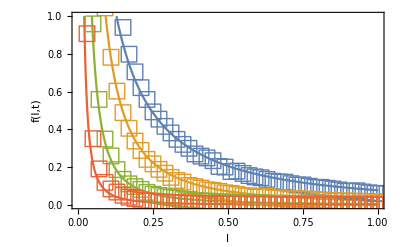

```mathematica
Subfigure["l","f(l,t)",With[{α=3/2,μ=-1,d=1},Plot[Evaluate@Table[Sin[π α/2]/π(d^(α/2)Exp[-μ t(1-α/2)])/(l^(α/2)(d+Exp[-μ t]l)),{t,1,7,2}],{l,0,1},Filling->None Table[n->{n+1},{n,3}],PlotRange->{Automatic,{0,1}}]],ListPlot[MapThread[{Last@#1,#2}&,{Outer[List,Sequence@@(MovingAverage[#,2]&/@{{"[◼]", "EvaluatePreviousCell"}}[][[1]])],#/(0.02Max[Total[#],1])&/@{{"[◼]", "EvaluatePreviousCell"}}[][[2]]},2],PlotMarkers->{"□",16}]]
```

### Figure 2

```mathematica
NestedMap[{#2,Re@P[#2,#1,1,3/2,1]}&,Range[4],Subdivide[-2,2,120-1]]//BinaryIcon["P(x,s)"]
```

```mathematica
NestedMap[With[{t=#1,x=#2},{x,InverseLaplace[P[x,#,1,3/2,1]&,t]}]&,Range[4],Subdivide[0,5,65-1]]//BinaryIcon["P(x,t)"]
```

```mathematica
Table[HistogramList[ParallelTable[Block[{x=1,i=0,dt=1.*^-3,α=3/2},For[i=0,(0<x)&&(i dt<t),i++,x+=dt^(1/α) RandomVariate[StableDistribution[α,0,0,1]]];Max[-10,Min[10,x]]],1200000],{-10,10,0.2},"PDF"],{t,1,4}]//BinaryIcon["empirical P(x,t)"]
```

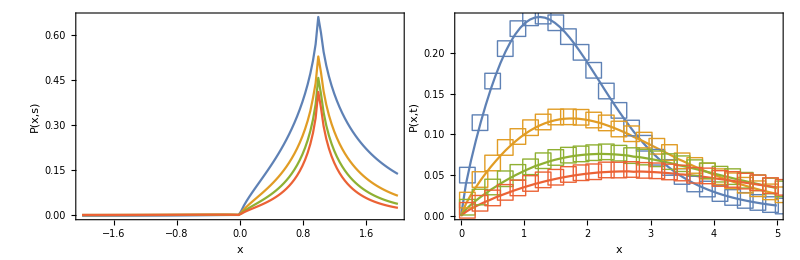

```mathematica
{ListLinePlot[{{"[◼]", "EvaluatePreviousCell"}}[5],PlotRange->All],ListLinePlot[Select[LessThan[.5]@*Last]/@{{"[◼]", "EvaluatePreviousCell"}}[3],PlotRange->All]~Show~ListPlot[Transpose@{MovingAverage[#[[1]],2],#[[2]]}&/@{{"[◼]", "EvaluatePreviousCell"}}[],PlotMarkers->{"□",16},PlotRange->{{0,5},{0,0.25}}]}//Figure[{"x","x"},{"P(x,s)","P(x,t)"}]
```

### Figure 3

```mathematica
Table[{β,Mean@ParallelTable[Block[{x=1,i=0,dt=0.001,α=3/2},For[i=0,0<x<2,i++,x+=dt^(1/α) RandomVariate[StableDistribution[α,β,0,1]]];i dt],120000]},{β,Subdivide[-1,1,32-1]}]//BinaryIcon["empirical FPTD"]
```

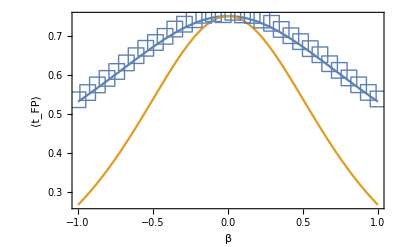

```mathematica
With[{α=3/2},Subfigure["β","⟨t_FP⟩",Plot[{(Cos[ArcTan[β Tan[π α/2]]]/Gamma[1+α]),(Cos[ArcTan[β Tan[π α/2]]]/Gamma[1+α])/(1+(β Tan[π α/2])^2)},{β,-1,1}],ListPlot[{{"[◼]", "EvaluatePreviousCell"}}[],PlotMarkers->{"□",16}]]]
```

```mathematica
NotebookSave[];CloseKernels[];
```